```mathematica
(*BASIC EVOLUTIONS ESERCIZIO 3a*)
```

```mathematica
subst[string_]:=StringReplace[string,{"AAB"->"BA","B"->"ABA"}]
```

```mathematica
subst["AABfrasCBettaAAB"]
```

BAfrasCABAettaBA

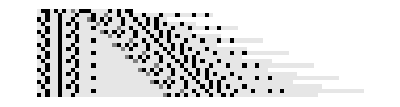

```mathematica
ArrayPlot[Characters[NestList[subst,"ABBABABACABBBAAAABABABB",20]]/.{"A"->0.1,"B"->1,"C"->0.5}]
```

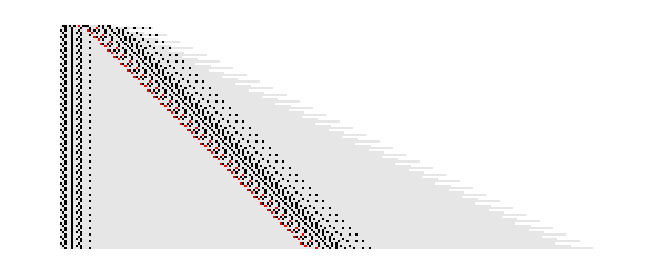

```mathematica
ArrayPlot[Characters[NestList[subst,"ABBABABACABBBAAAABABABB",100]]/.{"A"->0.1,"B"->1,"C"->Red}]
```

```mathematica
(*Esercizio 3b*)
```

```mathematica
substint[list_]:=Replace[list,{{x___,0,0,1,y___}:>{x,1,0,y},{x___,1,y___}:>{x,0,1,0,y}}]
```

```mathematica
seq10=Table[RandomInteger[{0,1}],{10}]
```

{0,0,1,0,1,0,1,0,1,1}

```mathematica
substint[seq10]
```

{1,0,0,1,0,1,0,1,1}

```mathematica
seq4=Table[RandomInteger[{0,1}],{4}]
```

{1,1,1,0}

```mathematica
substint[seq4]
```

{0,1,0,1,1,0}

```mathematica
{0,1,0}/.{x___,1,y___}:>{x,0,1,0,y}
```

{0,0,1,0,0}

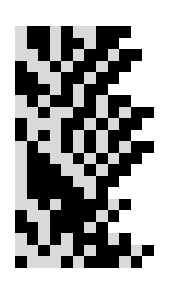

```mathematica
ArrayPlot[NestList[substint,Table[RandomInteger[{0,1}],{10}],20]/.{0->0.15}]
```

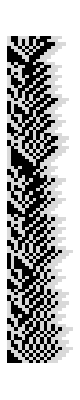

```mathematica
ArrayPlot[NestList[substint,Table[RandomInteger[{0,1}],{15}],100]/.{0->0.15}]
```